```mathematica
y[x_] := x^x
```

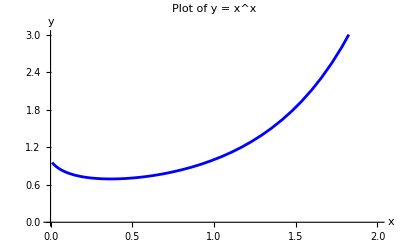

```mathematica
Plot[y[x], {x, 0.01, 3}, PlotRange -> {{0, 2}, {0, 3}},
     AxesLabel -> {"x", "y"}, PlotLabel -> "Plot of y = x^x", PlotStyle -> Blue]
```

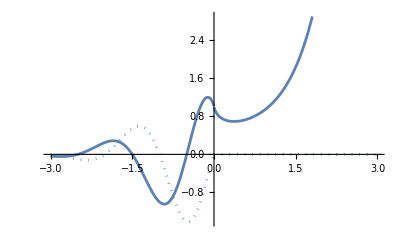

```mathematica
ReImPlot[x^x,{x,-3,3}]
```

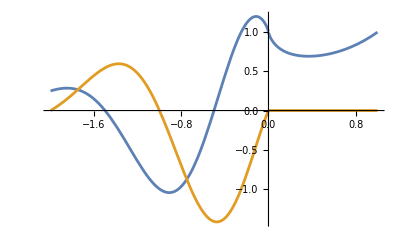

```mathematica
Plot[{Re[x^x],Im[x^x]},{x,-2,1}]
```

```mathematica
y'[x]
```

x^x (1+Log[x])

```mathematica
Solve[x^x (1+Log[x])==0,x]
```

{{x→1/ⅇ}}

```mathematica
ParametricPlot3D[{x,Re[x^x],Im[x^x]},{x,-4,2},PlotRange->All,ViewVertical->{0,1,0},BoxRatios->{2,1,1},ViewPoint->{12,2,12}]
```

-Graphics3D-

```mathematica
Manipulate[ParametricPlot3D[Evaluate@Table[{x,Re[Exp[(Log[Abs[x]]+2 I Pi k) x]],Im[Exp[(Log[Abs[x]]+2 I Pi k) x]]},{k,0,n}],{x,-4,2},PlotRange->All,ViewVertical->{0,1,0},BoxRatios->{2,1,1},ViewPoint->{12,2,12},AxesStyle->Thick,PlotLegends->Automatic],{n,0,10,1}]
```

```mathematica
Manipulate[Show[ParametricPlot3D[Evaluate@Table[{x,Re[Exp[(Log[Abs[x]]+2 I Pi k) x]],Im[Exp[(Log[Abs[x]]+2 I Pi k) x]]},{k,0,2}],{x,-4,2},PlotRange->All,AxesLabel->{"x","Real","Imaginary"},PlotLegends->Table["k = "<>ToString[k],{k,0,2}],PlotStyle->Table[ColorData["Rainbow"][k/5],{k,0,2}]],Graphics3D[Table[{ColorData["Rainbow"][k/5],PointSize[Large],Point[{sliderValue,Re[Exp[(Log[Abs[sliderValue]]+2 I Pi k) sliderValue]],Im[Exp[(Log[Abs[sliderValue]]+2 I Pi k) sliderValue]]}]},{k,0,2}]]],
{sliderValue,-4,2}]
```

```mathematica
Manipulate[GraphicsGrid[{{Show[ParametricPlot3D[Evaluate@Table[{x,Re[Exp[(Log[Abs[x]]+2 I Pi k) x]],Im[Exp[(Log[Abs[x]]+2 I Pi k) x]]},{k,0,2}],{x,-4,2},PlotRange->All,AxesLabel->{"x","Real","Imaginary"},PlotLegends->Table["k = "<>ToString[k],{k,0,2}],PlotStyle->Table[ColorData["Rainbow"][k/5],{k,0,2}]],Graphics3D[Table[{ColorData["Rainbow"][k/5],PointSize[Large],Point[{sliderValue,Re[Exp[(Log[Abs[sliderValue]]+2 I Pi k) sliderValue]],Im[Exp[(Log[Abs[sliderValue]]+2 I Pi k) sliderValue]]}]},{k,0,2}]]]},{Show[ParametricPlot[Evaluate@Table[{x,Re[Exp[(Log[Abs[x]]+2 I Pi k) x]]},{k,0,2}],{x,-4,2},PlotRange->All,AxesLabel->{"x","Real"},PlotStyle->Table[ColorData["Rainbow"][k/5],{k,0,2}]],Graphics[Table[{ColorData["Rainbow"][k/5],PointSize[Large],Point[{sliderValue,Re[Exp[(Log[Abs[sliderValue]]+2 I Pi k) sliderValue]]}]},{k,0,2}]]]},{Show[ParametricPlot[Evaluate@Table[{Re[Exp[(Log[Abs[x]]+2 I Pi k) x]],Im[Exp[(Log[Abs[x]]+2 I Pi k) x]]},{k,0,2}],{x,-4,2},PlotRange->All,AxesLabel->{"x","Imaginary"},PlotStyle->Table[ColorData["Rainbow"][k/5],{k,0,2}]],Graphics[Table[{ColorData["Rainbow"][k/5],PointSize[Large],Point[{Re[Exp[(Log[Abs[sliderValue]]+2 I Pi k) sliderValue]],Im[Exp[(Log[Abs[sliderValue]]+2 I Pi k) sliderValue]]}]},{k,0,2}]]]}}],{sliderValue,-4,2}]
```